```mathematica
R[t_]:=Subscript[R, I]+(2.02 Subscript[E, SN]/Subscript[p, 0])^(1/5)(t-ti)^(2/5);
D[R[t],t]
```

(0.460395 (ⅇ_SN/p_0)^(1/5))/(t-ti)^(3/5)

```mathematica
R2[t_,E_,p_,ti_]:=63072000000000000+(2 E/p)^(1/5)(t-ti)^(2/5);
R2[400*365*24*60*60*3,10^51,1.66*10^-24,400*365*24*60*60]
R3[t_,E_,p_,ti_]:=(0.4603946467498631 (E/p)^(1/5))/(t-ti)^(3/5)
R3[400*365*24*60*60+1,10^51,1.66*10^-24,400*365*24*60*60]
```

1.50925×10^19

4.16015×10^14

```mathematica
Plot[{R2[t,0.5*10^51,1.66*10^-26,400*365*24*60*60],R2[t,10^51,1.66*10^-24,400*365*24*60*60],R2[t,2*10^51,1.66*10^-22,400*365*24*60*60]},{t,400*365*24*60*60*1,400*365*24*60*60*10}]
```

-Graphics-

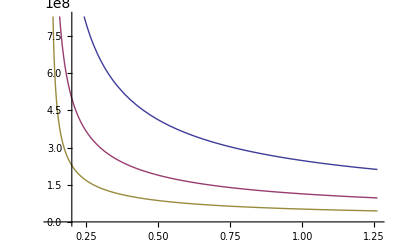

```mathematica
Plot[{R3[t,0.5*10^51,1.66*10^-26,400*365*24*60*60],R3[t,10^51,1.66*10^-24,400*365*24*60*60],R3[t,2*10^51,1.66*10^-22,400*365*24*60*60]},{t,400*365*24*60*60*1,400*365*24*60*60*10}]
```